## Lesson

Create an array using an abstract function (no variables):

```mathematica
Array[f,{2,3}]//Grid
```

f[1,1] | f[1,2] | f[1,3]
f[2,1] | f[2,2] | f[2,3]

Nest a function but supplying additional new values each time:

```mathematica
FoldList[Framed[f[#1,#2]]&,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

## Questions

Q1. Use Prime and Array to generate a list of the first 100 primes.

```mathematica
Array[Prime,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

Q2. Use Prime and Array to find successive differences between the first 100 primes.

```mathematica
Array[Prime[#+1]-Prime[#]&,100]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6}

Q3. Use Array and Grid to make a 10 by 10 addition table.

```mathematica
Grid[Array[#1+#2&,{10,10}]]
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

Q4. Use FoldList, Times and Range to successively multiply numbers up to 10 (making factorials).

```mathematica
FoldList[#1#2&,1,Range[10]]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

Q5. Use FoldList and Array to compute the successive products of the first 10 primes.

```mathematica
FoldList[#1#2&,1,Prime[Range[10]]]
```

{1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

Q6. Use FoldList to successively ImageAdd regular polygons with between 3 and 8 sides, and with opacity 0.2.

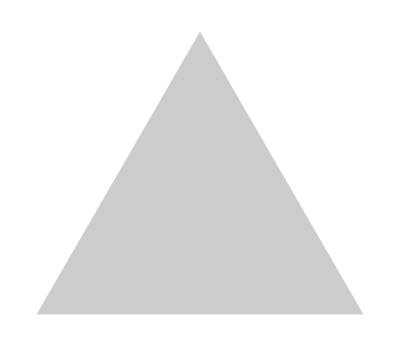
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FoldList[ImageAdd,Graphics[Style[RegularPolygon[#],Opacity[0.2]]]&/@Range[3,8]]
```

## Extended Questions

+Q1. Use Array to make a 10 by 10 grid where the leading diagonal and everything below it is 1 and the rest is 0.

```mathematica
Array[If[#1>=#2,1,0]&,{10,10}]
```

{{1,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0},{1,1,1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1,1,1}}